# nearest neighbor algorithm

## входные данные

### поле:

```mathematica
rows=40;
columns=60;
```

### дроны:

```mathematica
numberOfDrones=3;
turnsOfDrones=5000;
capacityOfDrones = 200;
```

### продукты:

```mathematica
numberOfProducts=5;
productsWeights = RandomInteger[{1,capacityOfDrones},numberOfProducts];
maxNumberOfProductsInWarehouses=100;
```

### склады:

```mathematica
numberOfWarehouses = 3;
```

```mathematica
Clear@generateWarehousesCoords
generateWarehousesCoords[rows_Integer,columns_Integer,number_Integer]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
warehousesCoords=generateWarehousesCoords[rows,columns,numberOfWarehouses]
```

{{28,23},{42,31},{27,10}}

```mathematica
productsInWarehouses=RandomInteger[maxNumberOfProductsInWarehouses,{numberOfWarehouses,numberOfProducts}]
```

{{67,87,58,99,13},{99,16,19,11,14},{98,11,100,14,26}}

```mathematica
totalNumberOfProducts=Total@productsInWarehouses
```

{264,114,177,124,53}

### заказы:

```mathematica
numberOfOrders =10;
```

```mathematica
Clear@generateOrdersCoords
generateOrdersCoords[rows_Integer,columns_Integer,number_Integer,warehouses:{{_Integer,_Integer}..}]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords~Join~warehousesCoords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
ordersCoords=generateOrdersCoords[rows,columns,numberOfOrders,warehousesCoords]
```

{{50,16},{37,17},{49,24},{42,14},{53,24},{3,31},{43,35},{40,21},{15,37},{26,8}}

```mathematica
Floor[Mean@totalNumberOfProducts/numberOfOrders]
```

14

```mathematica
Clear@generateOrders
generateOrders[numberOfOrders_Integer,totalNumberOfProducts_List]:=
RandomInteger[
Min[Floor[Mean@totalNumberOfProducts/numberOfOrders],3],
{numberOfOrders,Length@totalNumberOfProducts}
]
```

```mathematica
orders=generateOrders[numberOfOrders,totalNumberOfProducts]
```

{{0,2,3,0,3},{2,1,1,3,2},{1,3,1,1,0},{2,3,2,1,0},{3,0,1,1,2},{3,1,1,2,0},{0,2,0,2,3},{1,2,3,2,1},{2,3,3,3,1},{2,0,2,0,3}}

```mathematica
And@@(#>0&/@(totalNumberOfProducts-Total@orders))
```

True

### база данных:

```mathematica
data["drones"]
```

<|1→<|coords→{2,3},products→{0,0,0,0,0},score→0,nextWarehouse→-1,nextOrder→-1,nextTurns→-1|>,2→<|coords→{2,3},products→{0,0,0,0,0},score→0,nextWarehouse→-1,nextOrder→-1,nextTurns→-1|>,3→<|coords→{2,3},products→{0,0,0,0,0},score→0,nextWarehouse→-1,nextOrder→-1,nextTurns→-1|>|>

```mathematica
data=<|
"general"-> <|
"rows"->rows,
"columns"->columns,
"turns"-> turnsOfDrones,
"capacity"-> capacityOfDrones,
"numberOfDrones"->numberOfDrones,
"numberOfProducts"->numberOfProducts,
"numberOfWarehouses"-> numberOfWarehouses,
"numberOfOrders"-> numberOfOrders,
"weightsOfProducts"->productsWeights
|>,

"drones"->AssociationThread[Range@numberOfDrones->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧,"score"->#⟦3⟧,"nextWarehouse"->-1,"nextOrder"->-1,"nextTurns"->-1|>&/@Thread[{ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],ConstantArray[0,{numberOfDrones,numberOfProducts}],ConstantArray[0,numberOfDrones]}])],

"warehouses"->AssociationThread[Range@numberOfWarehouses->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧|>&/@Thread[{warehousesCoords,productsInWarehouses}])],

"orders"-><|
"order"->AssociationThread[Range@numberOfOrders->(<|"coords"->#⟦1⟧,"list"->#⟦2⟧,"turns"-> 0|>&/@Thread[{ordersCoords,orders}])],
"mask"->ConstantArray[0,numberOfOrders]
|>
|>;
```

## анализ данных

```mathematica
Values@data⟦"orders","order",All,"coords"⟧
```

{{50,16},{37,17},{49,24},{42,14},{53,24},{3,31},{43,35},{40,21},{15,37},{26,8}}

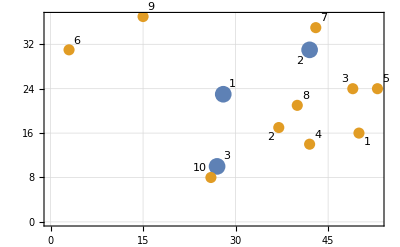

```mathematica
plot=ListPlot[{MapThread[Labeled,{Values@data⟦"warehouses",All,"coords"⟧,Range@data["general","numberOfWarehouses"]}],MapThread[Labeled,{Values@data⟦"orders","order",All,"coords"⟧,
Range@data["general","numberOfOrders"]}]},PlotTheme->"Detailed",PlotStyle->{PointSize[0.03],PointSize[0.02]}]
```

3 склада, расположенные в точках:

```mathematica
Values@data⟦"warehouses",All,"coords"⟧//Column
```

{28,23}
{42,31}
{27,10}

где первый склад - начальный, то есть откуда стартуют дроны. Есть 5 типов продуктов, которые весят соответственно:

```mathematica
data["general","weightsOfProducts"]//Column
```

124
64
164
17
133

каждого продукта на каждом складе соответственно:

```mathematica
Values@data⟦"warehouses",All,"products"⟧//Column
```

{67,87,58,99,13}
{99,16,19,11,14}
{98,11,100,14,26}

3 дрона, каждый из которых находится в первом складе и имеет грузоподъемность:

```mathematica
data["general","capacity"]
```

200

необходимо доставить 10 заказов на данные точки:

```mathematica
Values@data⟦"orders","order",All,"coords"⟧//Column
```

{50,16}
{37,17}
{49,24}
{42,14}
{53,24}
{3,31}
{43,35}
{40,21}
{15,37}
{26,8}

каждому клиенту необходимо соответсвующих товаров:

```mathematica
Values@data⟦"orders","order",All,"list"⟧//Column
```

{0,2,3,0,3}
{2,1,1,3,2}
{1,3,1,1,0}
{2,3,2,1,0}
{3,0,1,1,2}
{3,1,1,2,0}
{0,2,0,2,3}
{1,2,3,2,1}
{2,3,3,3,1}
{2,0,2,0,3}

## алгоритм

Для каждого дрона определяем ближайший склад, где можно пополнить запас продуктов, а также ближайшего клиента от этого склада.  Среди всех дронов выбираем того, у которого сумма длин двух расстояний наименьшая и выполняем им весь заказ или его часть. Так до тех пор, пока все заказы не будут выполнены.

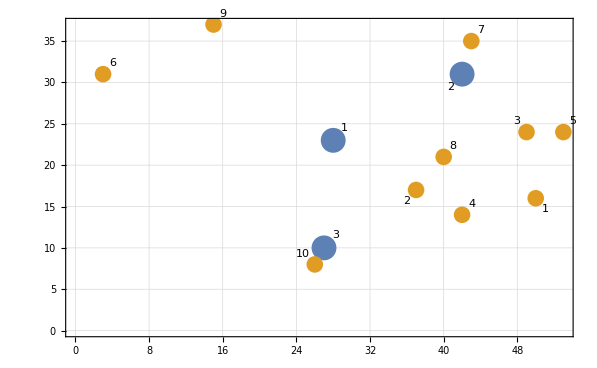

```mathematica
plot
```

```mathematica
(*нужно сделать проверку, чтобы дрон выбирал склад только в том случае, если на нем есть хотя бы один нужный товар*)
```

```mathematica
Clear@chooseNextDirection
chooseNextDirection[droneID_,data_Association]:=
Module[
{warehouse,order,warehouseCoords,tempData=data},
warehouse=First@MinimalBy[Normal@data⟦"warehouses",All,"coords"⟧,Ceiling@EuclideanDistance[Last@#,data["drones",droneID,"coords"]]&];
warehouseCoords = warehouse⟦2⟧;

order=First@MinimalBy[
Pick[Normal@data⟦"orders","order",All,"coords"⟧,data["orders","mask"],0],
Ceiling@EuclideanDistance[warehouseCoords,Last@#]&];

tempData["drones",droneID,"nextWarehouse"]=warehouse⟦1⟧;
tempData["drones",droneID,"nextOrder"]=order⟦1⟧;
tempData["drones",droneID,"nextTurns"]=Ceiling@EuclideanDistance[data["drones",droneID,"coords"],warehouseCoords]+Ceiling@EuclideanDistance[warehouseCoords,order⟦2⟧];

tempData
]
```

```mathematica
Clear@loadProducts
loadProducts[data_Association,warehouseID_Integer,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data,capacity =data["general","capacity"],weights=data["general","weightsOfProducts"],numberOfProduct},
Do[
numberOfProduct=
Min[
data⟦"warehouses",warehouseID,"products",i⟧,
data⟦"orders","order",orderID,"list",i⟧,
Quotient[capacity,weights⟦i⟧]
];
tempData⟦"warehouses",warehouseID,"products",i⟧-=numberOfProduct;
tempData⟦"drones",droneID,"products",i⟧+=numberOfProduct;
capacity-=weights⟦i⟧ numberOfProduct;

(*If[numberOfProduct>0,
Print["дрон ",droneID," загрузил ",numberOfProduct, " у.е. продукта ", i, " со склада ",warehouseID," для заказа ", orderID]];*)

If[capacity≤0,
Break[]
]

,{i,Length@weights}];
tempData
]
```

```mathematica
Clear@calculateTurns
calculateTurns[turn_Integer,data_Association]:=
With[{T=data["general","turns"]},Ceiling[(T-turn)/T 100]]
```

```mathematica
Clear@unloadProduct
unloadProduct[data_Association,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data},
tempData⟦"orders","order",orderID,"list"⟧-=tempData⟦"drones",droneID,"products"⟧;
tempData⟦"drones",droneID,"products"⟧=ConstantArray[0,data["general","numberOfProducts"]];

If[Total@tempData⟦"orders","order",orderID,"list"⟧==0,
tempData⟦"orders","mask",orderID⟧=1;
tempData["orders","order",orderID,"turns"]=calculateTurns[tempData["drones",droneID,"score"],tempData];
Print["заказ ",orderID, " полностью выполнен"]];
tempData
]
```

```mathematica
-Graphics-;
```

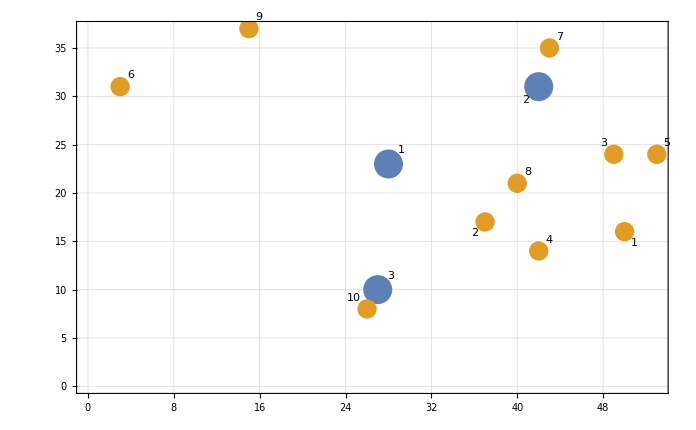

```mathematica
plot
```

```mathematica
Clear@solve
solve[data_Association]:=
Module[
{nextDrone,droneID,nextWarehouse,nextOrder,dronesWays,tempData=data},
While[
Times@@tempData["orders","mask"]≠1,

(*выбор дрона*)
Do[
tempData=chooseNextDirection[i,tempData]
,{i,tempData["general","numberOfDrones"]}
];
nextDrone=MinimalBy[tempData["drones"],#["score"]+#["nextTurns"]&];
droneID=First@Keys@nextDrone;
nextDrone=First@Values@nextDrone;
nextWarehouse=nextDrone["nextWarehouse"];
nextOrder=nextDrone["nextOrder"];

(*перемещение дрона на ближайший склад*)
tempData["drones",droneID,"coords"]=tempData["warehouses",nextWarehouse,"coords"];

(*погрузка товара*)
tempData=loadProducts[tempData,nextWarehouse,nextOrder,droneID];

(*перемещаение дрона к ближайшему клиенту*)
tempData["drones",droneID,"score"]+=tempData["drones",droneID,"nextTurns"];
If[tempData["drones",droneID,"score"]>tempData["general","turns"],
Print["превышено количество ходов"];
Break[]
];
tempData["drones",droneID,"coords"]=tempData["orders","order",nextOrder,"coords"];

(*разгрузка товара*)
tempData=unloadProduct[tempData,nextOrder,droneID]
];
tempData
]
```

```mathematica
solution=solve[data]
```

заказ 2 полностью выполнен

заказ 7 полностью выполнен

заказ 3 полностью выполнен

заказ 8 полностью выполнен

заказ 5 полностью выполнен

заказ 1 полностью выполнен

заказ 10 полностью выполнен

заказ 4 полностью выполнен

заказ 9 полностью выполнен

заказ 6 полностью выполнен

<|general→<|rows→40,columns→60,turns→5000,capacity→200,numberOfDrones→3,numberOfProducts→5,numberOfWarehouses→3,numberOfOrders→10,weightsOfProducts→{124,64,164,17,133}|>,drones→<|1→<|coords→{3,31},products→{0,0,0,0,0},score→498,nextWarehouse→1,nextOrder→6,nextTurns→54|>,2→<|coords→{3,31},products→{0,0,0,0,0},score→458,nextWarehouse→1,nextOrder→6,nextTurns→54|>,3→<|coords→{3,31},products→{0,0,0,0,0},score→448,nextWarehouse→1,nextOrder→6,nextTurns→54|>|>,warehouses→<|1→<|coords→{28,23},products→{61,83,52,92,10}|>,2→<|coords→{42,31},products→{93,6,12,6,5}|>,3→<|coords→{27,10},products→{94,8,96,11,23}|>|>,orders→<|order→<|1→<|coords→{50,16},list→{0,0,0,0,0},turns→95|>,2→<|coords→{37,17},list→{0,0,0,0,0},turns→100|>,3→<|coords→{49,24},list→{0,0,0,0,0},turns→99|>,4→<|coords→{42,14},list→{0,0,0,0,0},turns→94|>,5→<|coords→{53,24},list→{0,0,0,0,0},turns→97|>,6→<|coords→{3,31},list→{0,0,0,0,0},turns→91|>,7→<|coords→{43,35},list→{0,0,0,0,0},turns→99|>,8→<|coords→{40,21},list→{0,0,0,0,0},turns→98|>,9→<|coords→{15,37},list→{0,0,0,0,0},turns→92|>,10→<|coords→{26,8},list→{0,0,0,0,0},turns→95|>|>,mask→{1,1,1,1,1,1,1,1,1,1}|>|>

```mathematica
SortBy[solution⟦"orders","order",All,"turns"⟧,Value]
```

<|6→91,9→92,4→94,1→95,10→95,5→97,8→98,3→99,7→99,2→100|>